```mathematica
ClearAll["Global`*"]
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->18};
```

```mathematica
vs=4.303*1000/10; (*velocity in units of meV nm. Initial value at E=E_0.*)
gamma=24.75; (*energy in units of meV. Initial value at E=E_0.*)
(*gamma=10;*)
Omega0=Sqrt[3]/2((2.46/10)/(2Sin[1.05/360*2Pi/2]))^2;(*area in units of nm^2.*)
Lambda0=(8Pi)/(3*2.46/10)Sin[1.05/360*2Pi/2];(*wave vector at the boundary of mBZ in units of 1/nm.*)
E0=Sqrt[(vs*Lambda0)^2+gamma^2];(*energy in units of meV. Initial cutoff energy at the boundary of mBZ.*)
V0=Pi*10^2*24/Omega0;(*Coupling constant in units of meV. Initial value at E=E_0.*)
U0=57.95;(*Coupling constant in units of meV. Initial value at E=E_0.*)
W10=44.03;(*Coupling constant in units of meV. Initial value at E=E_0.*)
W30=50.20;(*Coupling constant in units of meV. Initial value at E=E_0.*)
J0=16.38;(*Coupling constant in units of meV. Initial value at E=E_0.*)
Jp0=J0;(*Coupling constant in units of meV. Initial value at E=E_0.*)
```

```mathematica
V0
```

48.3149

```mathematica
Omega0
```

156.056

```mathematica
(2.46/10)/(2Sin[1.05/360*2Pi/2])
```

13.4238

```mathematica
NDSolve[{J1'[t]*Omega0==-1/8 V0*J0*Omega0^2*(vs^2*t^2)/(Pi(vs^2*t^2+gamma^2)^(3/2))*t,J1[Lambda0]==0},{J1},{t,0,Lambda0}]
```

{{J1→InterpolatingFunction[…]}}

```mathematica
%36⟦1,1,2⟧
```

InterpolatingFunction[…]

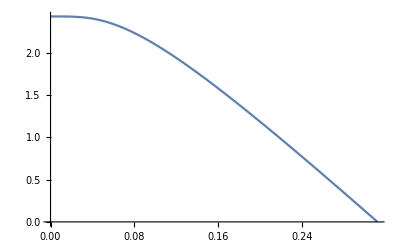

```mathematica
Plot[%37[x],{x,0.,0.31204274638213136}]
```

```mathematica
eqns={V'[t]*Omega0==((1-1/8)V[t]^2-V[t]*(W1[t]+W3[t])+1/8 V[t]*(W1[t]+W3[t])+1/4(W1[t]+W3[t])^2+1/8 V[t]*J[t]-1/32 J[t]*(W1[t]+W3[t]))*Omega0^2 *γ[t]^4/(Pi(v[t]^2*t^2+γ[t]^2)^(5/2))*t,
U'[t]*Omega0==((W1[t]-W3[t])^2+1/4 J[t]*(W1[t]-W3[t]))*Omega0^2*(v[t]^4*t^4)/(Pi(v[t]^2*t^2+γ[t]^2)^(5/2))*t+(-(2-1/4)U[t]*(W1[t]-W3[t])+2W1[t]*(W1[t]-W3[t])-1/4 U[t]*J[t]+1/8 J[t]*W1[t])*Omega0^2 *(γ[t]^2 v[t]^2*t^2)/(Pi(v[t]^2*t^2+γ[t]^2)^(5/2))*t+((1-1/4)U[t]^2-(2-1/4)U[t]*W1[t]+W1[t]^2)*Omega0^2 *γ[t]^4/(Pi(v[t]^2*t^2+γ[t]^2)^(5/2))*t,W1'[t]*Omega0==-1/8 V[t]*(W1[t]-W3[t])*Omega0^2*(v[t]^4*t^4)/(Pi(v[t]^2*t^2+γ[t]^2)^(5/2))*t+(1/8 V[t]*U[t]+(1-1/8)V[t]*(W1[t]-W3[t])-1/8 V[t]*W1[t]-W1[t]*(W1[t]-W3[t])+1/8 V[t]*J[t]-1/8 W1[t]*J[t])*Omega0^2 *(γ[t]^2 v[t]^2*t^2)/(Pi(v[t]^2*t^2+γ[t]^2)^(5/2))*t+(-(1-1/8-1/8)V[t]*U[t]+(1-1/8-1/8)V[t]*W1[t]+(1-1/8)U[t]*W1[t]-W1[t]^2)*Omega0^2 *γ[t]^4/(Pi(v[t]^2*t^2+γ[t]^2)^(5/2))*t,W3'[t]*Omega0==1/8 V[t]*(W1[t]-W3[t])*Omega0^2*(v[t]^4*t^4)/(Pi(v[t]^2*t^2+γ[t]^2)^(5/2))*t+(-1/8 V[t]*U[t]+V[t]*(W1[t]-W3[t])+1/8 V[t]*W1[t]-W3[t]*(W1[t]-W3[t])+1/8 V[t]*J[t]+1/8(W1[t]-W3[t])*J[t]-1/8 W3[t]*J[t])*Omega0^2 *(γ[t]^2 v[t]^2*t^2)/(Pi(v[t]^2*t^2+γ[t]^2)^(5/2))*t+(-(1-1/8)V[t]*U[t]+V[t]*W1[t]+(1-1/8)U[t]*W1[t]-W1[t]*W3[t]-1/8 U[t]*J[t]+1/8 W1[t]*J[t])*Omega0^2 *γ[t]^4/(Pi(v[t]^2*t^2+γ[t]^2)^(5/2))*t,J'[t]*Omega0==-1/8 V[t]*J[t]*Omega0^2*(v[t]^4*t^4)/(Pi(v[t]^2*t^2+γ[t]^2)^(5/2))*t+(-1/8 V[t]*U[t]-1/8*W3[t]^2-(1/8-1/8+1/8-1/8)W3[t]*J[t]-(1/8-1/2-1/8)J[t]^2-1/2 Jp[t]^2)*Omega0^2 *(γ[t]^2 v[t]^2*t^2)/(Pi(v[t]^2*t^2+γ[t]^2)^(5/2))*t+-1/8 U[t]*J[t]*Omega0^2 *γ[t]^4/(Pi(v[t]^2*t^2+γ[t]^2)^(5/2))*t,Jp'[t]*Omega0==1/8 V[t]*J[t]*Omega0^2*(v[t]^4*t^4)/(Pi(v[t]^2*t^2+γ[t]^2)^(5/2))*t+(1/8 V[t]*U[t]+1/8*W3[t]^2-(1/4+1/4)W3[t]*Jp[t]+J[t]*Jp[t])*Omega0^2 *(γ[t]^2 v[t]^2*t^2)/(Pi(v[t]^2*t^2+γ[t]^2)^(5/2))*t+1/8 U[t]*Jp[t]*Omega0^2 *γ[t]^4/(Pi(v[t]^2*t^2+γ[t]^2)^(5/2))*t,
v'[t]==-v[t]*1/(8Pi)*V[t]*Omega0*((v[t]^2*t^2+2 γ[t]^2)*t)/((v[t]^2*t^2+γ[t]^2)^(3/2)),γ'[t]==-γ[t]*1/(4Pi)*(W1[t]*t/((v[t]^2*t^2+γ[t]^2)^(1/2)))*Omega0,V[Lambda0]==V0,U[Lambda0]==U0,W1[Lambda0]==W10,W3[Lambda0]==W30,J[Lambda0]==J0,Jp[Lambda0]==Jp0,v[Lambda0]==vs,γ[Lambda0]==gamma};
sol=NDSolve[eqns,{V,U,W1,W3,J,Jp,v,γ},{t,0,Lambda0}]
```

{{V→InterpolatingFunction[…],U→InterpolatingFunction[…],W1→InterpolatingFunction[…],W3→InterpolatingFunction[…],J→InterpolatingFunction[…],Jp→InterpolatingFunction[…],v→InterpolatingFunction[…],γ→InterpolatingFunction[…]}}

```mathematica
pV=Plot[Evaluate[{V[t],U[t],W1[t],W3[t],J[t],Jp[t]}/. sol],{t,0,Lambda0},PlotRange->{{0,Lambda0},{0,60}},ImageSize->{250,180},PlotStyle->Automatic,FrameTicks->{{Table[{y,MaTeX[y,"DisplayStyle"->False]},{y,Range[0.,60.,10.]}],Table[{y,Spacer[0]},{y,Range[0.,60.,10.]}]},{Table[{x*Lambda0,MaTeX[x,"DisplayStyle"->False]},{x,Range[0.,1.,0.2]}],Table[{x*Lambda0,Spacer[0]},{x,Range[0.,1.,0.2]}]}},PlotLabels->MaTeX/@{"V","U","W_1","W_3","J","J_{+}"},Frame->True,FrameStyle->BlackFrame,FrameLabel->MaTeX/@{{"\\text{Energy (meV)}", ""},{"\\Lambda/\\Lambda_c",""}},BaseStyle->texStyle]
```

-Graphics-

```mathematica
Export["/Users/yihuang/Library/Mobile Documents/com~apple~CloudDocs/Documents/Project/RG_topological_heavy_fermion/RG/numerical_results.pdf",pV,"PDF"]
```

/Users/yihuang/Library/Mobile Documents/com~apple~CloudDocs/Documents/Project/RG_topological_heavy_fermion/RG/numerical_results.pdf

```mathematica
Plot[Evaluate[{J[t]}/. sol],{t,0,Lambda0},PlotStyle->Automatic,PlotLabels->{"J"}]
```

-Graphics-

```mathematica
Plot[Evaluate[{v[t]}/. sol],{t,0,Lambda0},PlotStyle->Automatic,PlotLabels->{"v"}]
```

-Graphics-

```mathematica
Plot[Evaluate[{γ[t]}/. sol],{t,0,Lambda0},PlotStyle->Automatic,PlotLabels->{"γ"}]
```

-Graphics-

```mathematica
vSol=Evaluate[{v}/. sol][[1]][[1]]
gammaSol=Evaluate[{γ}/. sol][[1]][[1]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

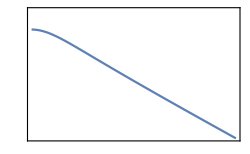

```mathematica
pvstar=Plot[vSol[t]/vSol[Lambda0],{t,0,Lambda0},PlotRange->{{0,Lambda0},{1,1.25}},ImageSize->{250,180},PlotStyle->Automatic,FrameTicks->{{Table[{y,MaTeX[y,"DisplayStyle"->False]},{y,Range[1,1.25,0.05]}],Table[{y,Spacer[0]},{y,Range[1,1.25,0.05]}]},{Table[{x*Lambda0,MaTeX[x,"DisplayStyle"->False]},{x,Range[0.,1.,0.2]}],Table[{x*Lambda0,Spacer[0]},{x,Range[0.,1.,0.2]}]}},Frame->True,FrameStyle->BlackFrame,(*FrameLabel->MaTeX/@{{"v_{\\star}(\\Lambda)/v_{\\star}(\\Lambda_c)", ""},{"\\Lambda/\\Lambda_c",""}},*)BaseStyle->texStyle]
```

```mathematica
Export["/Users/yihuang/Library/Mobile Documents/com~apple~CloudDocs/Documents/Project/RG_topological_heavy_fermion/RG/v_star_RG.eps",pvstar,"EPS"]
```

/Users/yihuang/Library/Mobile Documents/com~apple~CloudDocs/Documents/Project/RG_topological_heavy_fermion/RG/v_star_RG.eps

```mathematica
gammaSol[0]/gammaSol[Lambda0]
```

1.344

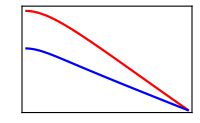

```mathematica
pgamma=Plot[{gammaSol[t]/gammaSol[Lambda0],vSol[t]/vSol[Lambda0]},{t,0,Lambda0},PlotRange->{{0,Lambda0},{1,1.35}},ImageSize->{200,150},PlotStyle->{{Red},{Blue}},FrameTicks->{{Table[{y,MaTeX[y,"DisplayStyle"->False]},{y,Range[1,1.35,0.1]}],Table[{y,Spacer[0]},{y,Range[1,1.35,0.1]}]},{Table[{x*Lambda0,MaTeX[x,"DisplayStyle"->False]},{x,Range[0.,1.,0.2]}],Table[{x*Lambda0,Spacer[0]},{x,Range[0.,1.,0.2]}]}},Frame->True,FrameStyle->BlackFrame,FrameLabel->MaTeX/@{{"", ""},{"\\Lambda/\\Lambda_c",""}},BaseStyle->texStyle]
```

```mathematica
Export["/Users/yihuang/Library/Mobile Documents/com~apple~CloudDocs/Documents/Project/RG_topological_heavy_fermion/RG/gamma_RG.eps",pgamma,"EPS"]
```

/Users/yihuang/Library/Mobile Documents/com~apple~CloudDocs/Documents/Project/RG_topological_heavy_fermion/RG/gamma_RG.eps

#### Leading diagrams

```mathematica
eqns={U'[t]*Omega0==1/Pi((v[t]^2*t^2(W1[t]-W3[t])*Omega0 + γ[t]^2 W1[t]*Omega0 )^2)/((v[t]^2*t^2+γ[t]^2)^(5/2))*t+1/(8Pi)((J[t]+J1[t])*Omega0*(v[t]^4*t^4(W1[t]-W3[t])*Omega0))/((v[t]^2*t^2+γ[t]^2)^(5/2))*t,W1'[t]*Omega0==-1/(8Pi)V0*Omega0*(((v[t]^2*t^2)t)/((v[t]^2*t^2+γ[t]^2)^(3/2))(W1[t]-W3[t])+((γ[t]^2)t)/((v[t]^2*t^2+γ[t]^2)^(3/2))W1[t])*Omega0,W3'[t]*Omega0==1/(8Pi)V0*Omega0*(((v[t]^2*t^2)^2 t)/((v[t]^2*t^2+γ[t]^2)^(5/2))(W1[t]-W3[t])+((v[t]^2*t^2)(γ[t]^2)t)/((v[t]^2*t^2+γ[t]^2)^(5/2))W1[t])*Omega0,J'[t]*Omega0==-1/(8Pi)V0*Omega0*(((v[t]^2*t^2)^2 t)/((v[t]^2*t^2+γ[t]^2)^(5/2))*J[t]+t/((v[t]^2*t^2+γ[t]^2)^(1/2))J1[t])*Omega0,J1'[t]*Omega0==-1/(8Pi)V0*Omega0*(((v[t]^2*t^2)t)/((v[t]^2*t^2+γ[t]^2)^(3/2))*J[t]+((v[t]^2*t^2)t)/((v[t]^2*t^2+γ[t]^2)^(3/2))*J1[t])*Omega0,U1'[t]*Omega0==-1/(8Pi)(((v[t]^2*t^2)^2 t)/((v[t]^2*t^2+γ[t]^2)^(5/2))J[t]^2+(v[t]^2*t^2*t)/((v[t]^2*t^2+γ[t]^2)^(3/2))2J[t]*J1[t]+t/((v[t]^2*t^2+γ[t]^2)^(1/2))J1[t]^2)*Omega0^2,v'[t]==-v[t]*1/(8Pi)*V0*Omega0*((v[t]^2*t^2+2 γ[t]^2)*t)/((v[t]^2*t^2+γ[t]^2)^(3/2)),γ'[t]==-γ[t]*1/(4Pi)*(W1[t]*t/((v[t]^2*t^2+γ[t]^2)^(1/2))+J1[t]*t/((v[t]^2*t^2+γ[t]^2)^(1/2)))*Omega0,U[Lambda0]==U0,W1[Lambda0]==W10,W3[Lambda0]==W30,J[Lambda0]==J0,J1[Lambda0]==0,U1[Lambda0]==0,v[Lambda0]==vs,γ[Lambda0]==gamma};
sol=NDSolve[eqns,{U,W1,W3,J,J1,U1,v,γ},{t,0,Lambda0}]
```

{{U→InterpolatingFunction[…],W1→InterpolatingFunction[…],W3→InterpolatingFunction[…],J→InterpolatingFunction[…],J1→InterpolatingFunction[…],U1→InterpolatingFunction[…],v→InterpolatingFunction[…],γ→InterpolatingFunction[…]}}

```mathematica
Plot[Evaluate[{U[t],W1[t],W3[t],J[t],J1[t],U1[t]}/. sol],{t,0,Lambda0},PlotStyle->Automatic,PlotLabels->{"U","W1","W3","J","J1","U1"}]
```

-Graphics-

```mathematica
Plot[Evaluate[{γ[t]}/. sol],{t,0,Lambda0},PlotStyle->Automatic,PlotLabels->{"γ"}]
```

-Graphics-

```mathematica
Plot[Evaluate[{v[t]}/. sol],{t,0,Lambda0},PlotStyle->Automatic,PlotLabels->{"v"}]
```

-Graphics-

```mathematica
Plot[Evaluate[{J1[t],U1[t]}/. sol],{t,0,Lambda0},PlotStyle->Automatic,PlotLabels->{"J1","U1"}]
```

-Graphics-